```mathematica
L[μ_]:=(b1+μ*s1)^n1*Exp[-(b1+μ*s1)]*(b2+μ*s2)^n2*Exp[-(b2+μ*s2)]
L[μ]
L[0]
q0[μ_]:=FullSimplify[-2*PowerExpand@Log[L[0]/L[μ]]]
q0[μ]
a0[μ_]:=FullSimplify[q0[μ]/.{n1->b1+μ*s1,n2->b2+μ*s2}]
a0[μ]
```

ⅇ^(-b1-b2-s1 μ-s2 μ) (b1+s1 μ)^n1 (b2+s2 μ)^n2

b1^n1 b2^n2 ⅇ^(-b1-b2)

-2 ((s1+s2) μ+n1 Log[b1]+n2 Log[b2]-n1 Log[b1+s1 μ]-n2 Log[b2+s2 μ])

-2 ((s1+s2) μ+(b1+s1 μ) Log[b1]+(b2+s2 μ) Log[b2]-(b1+s1 μ) Log[b1+s1 μ]-(b2+s2 μ) Log[b2+s2 μ])

```mathematica
t1[μ_]:=a0[μ]/.{b1->100,b2->100,s1->1,s2->0}
t2[μ_]:=a0[μ]/.{b1->100,b2->100,s1->0.5,s2->0.5}
FullSimplify[t1[μ]]
FullSimplify[t2[μ]]
```

-2 (μ+(100+μ) Log[100]-(100+μ) Log[100+μ])

-1842.07-11.2103 μ+(400.+2. μ) Log[100.+0.5 μ]

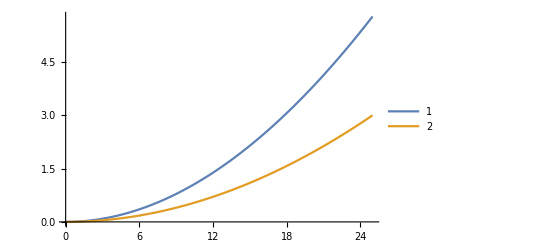

```mathematica
Plot[{t1[μ],t2[μ]},{μ,0,25},PlotLegends->Automatic]
```

```mathematica
FindRoot[t1[μ]-1,{μ,0,25}]
FindRoot[t2[μ]-1,{μ,0,25}]
```

{μ→10.1653}

{μ→14.3078}